```mathematica
Exit
```

```mathematica
(*MM=2*1024;
NN=2*1024;
KK=2*1024;*)

MM=128;
NN=128;
KK=256;

gRows=16;
gCols=16;

(*gRows=8;
gCols=8;
*)
vLen=4;

gVerCount=NN/(vLen gCols);
gHorCount=MM/(vLen  gRows);

tileM=vLen gRows;
tileN=vLen gCols;
tileK =((32768/4)/(tileM+tileN))/2;

(*A=RandomReal[{-1,1},{MM KK}];
B=RandomReal[{-1,1},{KK NN}];*)

A=ConstantArray[0.,{MM,KK}];
B=ConstantArray[0.,{KK, NN}];

Amask=ConstantArray[0,{MM KK}];
Bmask=ConstantArray[0,{KK NN}];

A[[120,40]]=1.;
B[[67,120]]=1.;
CC=RandomReal[0.,{MM  NN}];
Cmask=ConstantArray[0,{MM NN}];

CTrue=Transpose[B.A];

A=Flatten[A];
B=Flatten[B];

Ashared=ConstantArray[0.,{tileK,tileM}];
Bshared=ConstantArray[0.,{tileN,tileK}];
```

```mathematica
GroupId[gi_,gj_]:=gVerCount gj+gi;
ThreadId[gi_,gj_,li_,lj_]:=(gRows gCols)*GroupId[gi,gj]+gRows lj+li;
Coordinates[gi_,gj_,li_,lj_]:={gRows gi+li,gCols gj+lj};

ThreadJob[gi_,gj_,li_,lj_]:=Module[{i,iend,j,jend,k,kend,Atk,Btk,Ctile},
Do[
jend=jbegin+tileN;
Do[
iend=ibegin+tileM;

Atk=ConstantArray[0.,{vLen}];
Btk=ConstantArray[0.,{vLen}];
Ctile=ConstantArray[0.,{vLen,vLen}];

Do[
kend=kbegin+tileK;

Do[
Do[
Ashared[[k-kbegin+1,i-ibegin+1]] = A[[MM k +i+1]];

Amask[[MM k +i+1]]=ThreadId[gi,gj,li,lj];

,{i,ibegin+li,iend-1,gRows}];
,{k,kbegin+lj,kend-1,gCols}];



Do[
Do[
Bshared[[j-jbegin+1,k-kbegin+1]] = B[[KK j +k+1]];

Bmask[[KK j +k+1]]=ThreadId[gi,gj,li,lj];

,{k,kbegin+li,kend-1,gRows}];
,{j,jbegin+lj,jend-1,gCols}];

Do[
Do[Atk[[ti+1]]=Ashared[[tk+1]][[gRows ti+li+1]];,{ti,0,vLen-1}];

Do[Btk[[tj+1]]=Bshared[[gCols tj+lj+1]][[tk+1]];,{tj,0,vLen-1}];

Do[
Do[
Ctile[[tj+1]][[ti+1]]+=Atk[[ti+1]] Btk[[tj+1]];
,{ti,0,vLen-1}];
,{tj,0,vLen-1}];

,{tk,0,tileK-1}];


,{kbegin,0,KK-1,tileK}];

Do[
j=jbegin+gCols tj+lj;
Do[
i=ibegin+gRows ti+li;
(*Print[{i,j}];*)
CC[[MM j+i+1]]=Ctile[[tj+1]][[ti+1]];
(*Cmask[[MM j+i+1]]=GroupId[gi,gj];*)
Cmask[[MM j+i+1]]=ThreadId[gi,gj,li,lj];

(*Sow[{i,j},ThreadId[gi,gj,li,lj]];*)
Sow[{i,j},ThreadId[gi,gj,li,lj]];
,{ti,0,vLen-1}];
,{tj,0,vLen-1}];

,{ibegin,gi tileM,MM-1,gVerCount tileM}];
,{jbegin,gj tileN,NN-1,gHorCount tileN}];
];

ThreadGroupJob[gi_,gj_]:=Module[{},
Ashared=ConstantArray[0.,{tileK,tileM}];
Bshared=ConstantArray[0.,{tileN,tileK}];
Print[{gi,gj}];
Do[
Do[

ThreadJob[gi,gj,li,lj];
,{li,0,gRows-1}];
,{lj,0,gCols-1}];
];

GridJob[]:=Module[{},
Do[
Do[
ThreadGroupJob[gi,gj];
,{gi,0,gVerCount-1}];
,{gj,0,gHorCount-1}];
];
```

```mathematica
ConstantArray[0.,{tileK,tileM}]//Dimensions
```

{32,64}

```mathematica
ThreadJob[2,1,0,0]
```

```mathematica
tileM
```

64

```mathematica
tileN
```

64

```mathematica
tileK
```

32

```mathematica
ThreadGroupJob[2,4]
```

{2,4}

```mathematica
GridJob[]
```

```mathematica
trajectories=Association[Reap[ThreadGroupJob[2,1],_,Rule][[2]]];
```

{2,1}

{2,1}

{2,1}

«1 more identical outputs»

trajectories
{2,1}

```mathematica
trajectories=Association[Reap[GridJob[],_,Rule][[2]]];
```

{0,0}

{1,0}

{2,0}

{3,0}

{4,0}

{5,0}

$Aborted

```mathematica
trajectories[0]
```

Missing[KeyAbsent,0]

```mathematica
Show[
Graphics[{Black,Line[#],Red,Point[#]}]&[trajectories[0]],
Graphics[{Black,Line[#],Red,Point[#]}]&[trajectories[1]],
Graphics[{Black,Line[#],Red,Point[#]}]&[trajectories[2]]
]
```

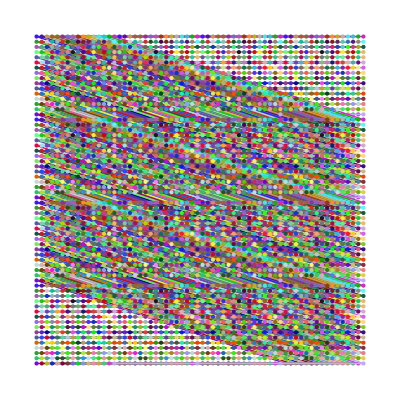

```mathematica
Show[Graphics[{RandomColor[],Point[#],Line[#]}]&/@Values@trajectories]
```

```mathematica
ListLinePlot[trajectories]
```

-Graphics-

```mathematica
MM
```

128

```mathematica
MatrixPlot[Transpose@ArrayReshape[Amask,{KK,MM}],ColorFunction->"Rainbow",FrameTicks->All,ImageSize->1/2{KK,MM},MaxPlotPoints->∞]
MatrixPlot[Transpose@ArrayReshape[Bmask,{NN,KK}],ColorFunction->"Rainbow",FrameTicks->All,ImageSize->1/2{NN,KK},MaxPlotPoints->∞]
MatrixPlot[Transpose@ArrayReshape[Cmask,{MM,NN}],ColorFunction->"Rainbow",FrameTicks->All,ImageSize->1/2{MM,NN},MaxPlotPoints->∞]
```

-Graphics-

-Graphics-

-Graphics-